Задание переменных и функций:
x=1; F[x_]:=x^2;
Применение функции:
	 F@x                        (⇔F[x])
		x//F                    (⇔F[x])
		F@@{x,y,z}   (⇔F[x,y,z])
		F/@{x,y,z}   (⇔{F[x],F[y],F[z]})
Анонимные функции:
	#^2&     (⇔F[x_]:=x^2)

# Графики

```mathematica
tab=100Sin/@Range[7]
```

{100 Sin[1],100 Sin[2],100 Sin[3],100 Sin[4],100 Sin[5],100 Sin[6],100 Sin[7]}

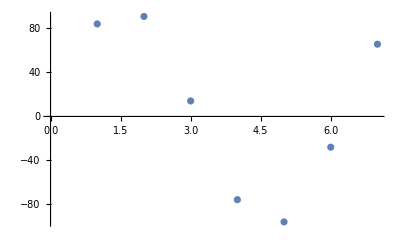

```mathematica
ListPlot[tab]
```

```mathematica
xs=10Range[7]
```

{10,20,30,40,50,60,70}

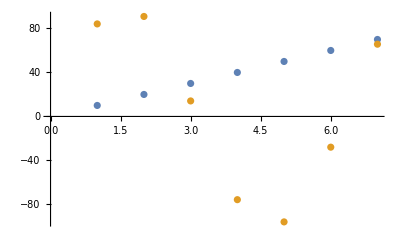

```mathematica
ListPlot[{xs,tab}]
```

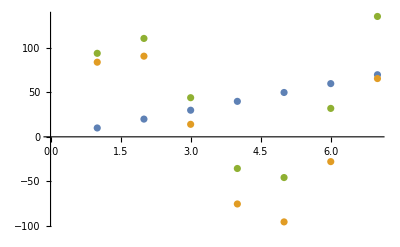

```mathematica
ListPlot[{xs,tab,xs+tab}]
```

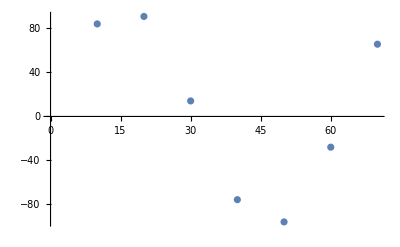

```mathematica
ListPlot[{xs,tab}ᵀ]
```

```mathematica
{xs,tab}
{xs,tab}ᵀ
```

{{10,20,30,40,50,60,70},{100 Sin[1],100 Sin[2],100 Sin[3],100 Sin[4],100 Sin[5],100 Sin[6],100 Sin[7]}}

{{10,100 Sin[1]},{20,100 Sin[2]},{30,100 Sin[3]},{40,100 Sin[4]},{50,100 Sin[5]},{60,100 Sin[6]},{70,100 Sin[7]}}

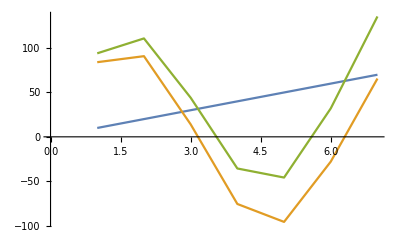

```mathematica
ListLinePlot[{xs,tab,xs+tab}]
```

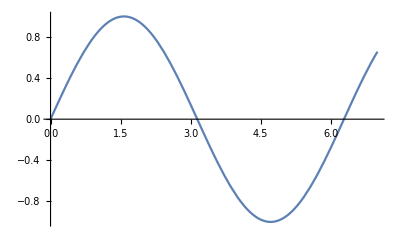

```mathematica
Plot[Sin[x],{x,0,7}]
```

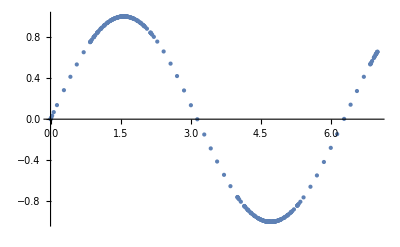

```mathematica
Plot[Sin[x],{x,0,7}]/.Line->Point
```

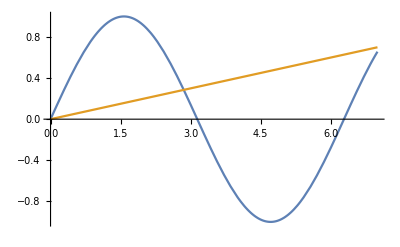

```mathematica
Plot[{Sin[x],x/10},{x,0,7}]
```

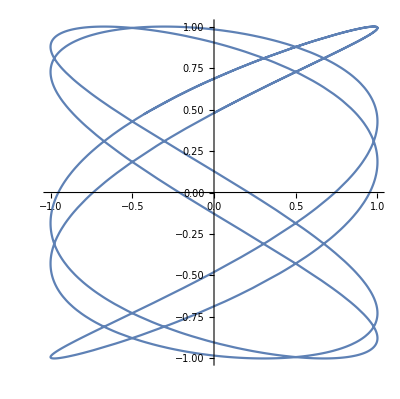

```mathematica
ParametricPlot[{Sin[5 t],Sin[3t+.5]},{t,0,7}]
```

Plot[]
ListPlot[]
ParametricPlot[]
ContourPlot[]
LogLogPlot[]
PolarPlot[]
…
Plot3D[]
…

```mathematica
%4
```

{10 Sin[1],10 Sin[2],10 Sin[3],10 Sin[4],10 Sin[5],10 Sin[6],10 Sin[7]}

# Подстановки

x=1 (⇔Set[x,1]    — задание глобального правила)
x→1 (⇔Rule[x,1] — задание локального правила)
x^2/.x→1 (⇔ ReplaceAll[x^2,x→1] — применение локального правила)
x^2+y/.{x→y,y→4}    (однократное применение списка правил)

x^2+y//.{x→y,y→4} (⇔ ReplaceRepeated[…] — полное применение списка правил)
x:>1 (⇔RuleDelayed[x,1] — задание локального правила без вычисления правой части)

```mathematica
x->3
```

x→3

```mathematica
rule=x->2
```

x→2

```mathematica
rule
```

x→2

```mathematica
x
```

x

```mathematica
?x
```

Global`x

```mathematica
x/.rule
```

2

```mathematica
x^2/.rule
```

4

```mathematica
x^2+Sin[x]/.x->√y
```

y+Sin[√y]

```mathematica
a+b/.Plus->Times
```

a b

```mathematica
Times@@(a+b)
```

a b

```mathematica
(a+b)^2/.Plus->Times
```

a^2 b^2

```mathematica
Times@@((a+b)^2)
```

2 (a+b)

# Решение Уравнений

```mathematica
Solve[x^2+x==1,x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

a==b (⇔Equal[a,b] — оператор сравнения)

```mathematica
Solve[{x^2+y==4,y^2==1},{x,y}]
```

{{x→-√3,y→1},{x→√3,y→1},{x→-√5,y→-1},{x→√5,y→-1}}

```mathematica
sol=Solve[{x^2+y==4,y^2==1},{x,y}];
```

```mathematica
x/.sol
```

{-√3,√3,-√5,√5}

```mathematica
y/.sol
```

{1,1,-1,-1}

```mathematica
x+2y/.sol
```

{2-√3,2+√3,-2-√5,-2+√5}

Solve[]
NSolve[] 
FindRoot[]
 
DSolve[] 
NDSolve[]

# Параметры графиков

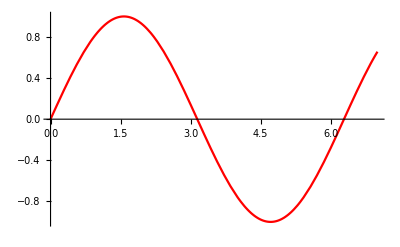

```mathematica
Plot[Sin[x],{x,0,7},PlotStyle->Red]
```

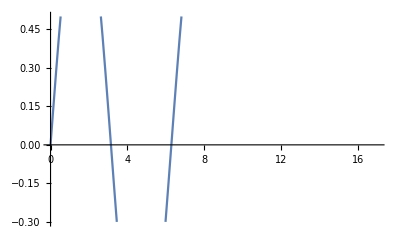

```mathematica
Plot[Sin[x],{x,0,7},PlotRange->{{0,17},{-.3,.5}}]
```

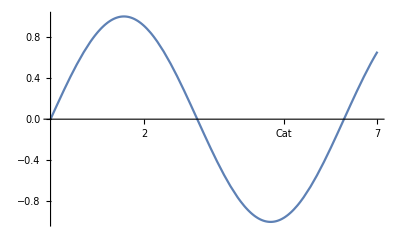

```mathematica
Plot[Sin[x],{x,0,7},Ticks->{{2,{5,"Cat"},7},Automatic}]
```

Полный список настроек в справке функции :